## A reanalysis of the SH0ES data for H_0. Baseline model in the absence of the inverse distance ladder constraint

## Setting the directory

```mathematica
SetDirectory[NotebookDirectory[]];  
 Off[Inverse::luc];
```

## Parameters - Data - Matrix of Measurements Y - Matrix of Parameters qpar

```mathematica
ydata=Import[".\\data\\ally_shoes_ceph_topantheonwt6.0_112221.fits","RawData"] [[1]]//Normal;
```

```mathematica
Y=ydata;(* This is the matrix of measurements*)
```

```mathematica
Length[Y]
```

3492

```mathematica
(* The system is Y=L qpar. qpar has single column with 47 entries. Entry 45 is useless and does not appear anywhere but we keep it for completeness as it has been included in the fits data but it is not mentioned in Riess 21. *)
```

```mathematica
qpar={"mu_{M101}","mu_{M1337}","mu_{N0691}","mu_{N1015}","mu_{N0105}","mu_{N1309}","mu_{N1365}","mu_{N1448}","mu_{N1559}","mu_{N2442}","mu_{N2525}","mu_{N2608}","mu_{N3021}","mu_{N3147}","mu_{N3254}","mu_{N3370}","mu_{N3447}","mu_{N3583}","mu_{N3972}","mu_{N3982}","mu_{N4038}","mu_{N4424}","mu_{N4536}","mu_{N4639}","mu_{N4680}","mu_{N5468}","mu_{N5584}","mu_{N5643}","mu_{N5728}","mu_{N5861}","mu_{N5917}","mu_{N7250}","mu_{N7329}","mu_{N7541}","mu_{N7678}","mu_{N0976}","mu_{U9391}","Delta mu_{Ν4258}","M_H^W","Delta mu_{LMC}","mu_{M31}","b_W","M_B","Z_W","X","Delta zp","5 log H_0"}; 
(* The length of the parameter vector is longer than expected due to an extra parameter X that has benn included but play no role at all and is not mentioned in their paper. The expected length is 46. *)
```

## Equation (or Design) Matrix L

```mathematica
ldata=Import[".\\data\\alll_shoes_ceph_topantheonwt6.0_112221.fits","RawData"]//Normal;
```

```mathematica
trL=ldata[[1,2]]//Normal;
```

```mathematica
L=Transpose[trL](* Y = L.qpar . L denotes the original model used by the SH0ES team*)
```

{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.164088,0.,0.0525404,0.,0.,0.},3490,{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,-1.}}
 |  |  |  |

```mathematica
MatrixForm[L]
```

(1)
 |  |  |  |

## Measurement Error Matrix

```mathematica
cdata=Import[".\\data\\allc_shoes_ceph_topantheonwt6.0_112221.fits","RawData"];
```

```mathematica
Call=cdata[[1]]//Normal;(* This is the Covariance matrix*)
```

## Best fit parameter values and the 1 sigma errors

```mathematica
InvCall=Inverse[Call];
```

```mathematica
sigma=Inverse[trL.InvCall.L];
```

```mathematica
(* These are the best fit parameter values. These formulas are proven in https://people.duke.edu/~hpgavin/SystemID/CourseNotes/linear-least-squres.pdf eq. 11 *)
```

```mathematica
qbf=sigma.(trL.InvCall.Y)
```

{29.1596,32.9156,32.8222,32.6178,34.4934,32.509,31.3254,31.2951,31.4608,31.4652,32.0114,32.6278,32.3916,33.0908,32.4031,32.1425,31.9443,32.7899,31.7072,31.6382,31.6338,30.8239,30.8355,31.7874,32.5468,33.1873,31.8655,30.5084,32.9159,32.2052,32.3369,31.606,33.2692,32.5797,33.2669,33.5439,32.816,-0.0127018,-5.89352,0.0100843,24.3714,-0.0135244,-19.2529,-0.216585,0.,-0.0738103,9.31789}

```mathematica
(* the  1 sigma errors for the  parameters *)
```

```mathematica
sigmadiag=Table[Sqrt[sigma[[i,i]]],{i,1,47}]
```

{0.0387512,0.0821192,0.0876812,0.0600767,0.119358,0.050678,0.0500633,0.0357285,0.0516334,0.0546367,0.0606591,0.114843,0.096619,0.085483,0.0564277,0.0456347,0.0333316,0.0634223,0.0676238,0.0561344,0.0800615,0.108035,0.0479758,0.0713565,0.147044,0.0485086,0.0453757,0.0423385,0.103193,0.0756345,0.0769425,0.103313,0.070201,0.0843556,0.0832043,0.0823285,0.0544389,0.0217961,0.0180529,0.0194059,0.0686838,0.0149153,0.0288987,0.0452084,0.0000316228,0.0105856,0.0299413}

## Structure of system (see qpar for parameter names).

```mathematica
cep=1;
Y[[cep]];
L[[cep]] (* 2150 Cepheids in non-anchor SnIa hosts *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.164088,0.,0.0525404,0.,0.,0.}

23.1523==0.-0.164088 b_W+1. M_H^W+1. mu_{M101}+0.0525404 Z_W

0.192417

```mathematica
cep=2;
Y[[cep]];
L[[cep]] (* 2150 Cepheids in non-anchor SnIa hosts *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,-0.162824,0.,0.0890804,0.,0.,0.}

22.4195==0.-0.162824 b_W+1. M_H^W+1. mu_{M101}+0.0890804 Z_W

0.386483

```mathematica
cep=2150;
Y[[cep]];
L[[cep]] (* 2150 Cepheids in non-anchor SnIa hosts *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.,0.,0.431993,0.,-0.25934,0.,0.,0.}

27.3094==0.+0.431993 b_W+1. M_H^W+1. mu_{U9391}-0.25934 Z_W

0.136279

```mathematica
cep=2151;
Y[[cep]];
L[[cep]] (* 443 Cepheids in the anchor N4258 *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,0.,0.608081,0.,-0.0613496,0.,0.,0.}

-6.04478==0.+0.608081 b_W+1. Delta mu_{Ν4258}+1. M_H^W-0.0613496 Z_W

0.185953

```mathematica
cep=2150+443;
Y[[cep]];
L[[cep]] (* 443 Cepheids in the anchor N4258 *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,0.,0.591806,0.,-0.13435,0.,0.,0.}

-5.89048==0.+0.591806 b_W+1. Delta mu_{Ν4258}+1. M_H^W-0.13435 Z_W

0.0247187

```mathematica
cep=2150+443+1;
Y[[cep]];
L[[cep]] (* 55 Cepheids in the anchor M31 *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.747707,0.,-0.12,0.,0.,0.}

18.6692==0.+0.747707 b_W+1. M_H^W+1. mu_{M31}-0.12 Z_W

0.009604

```mathematica
cep=2150+443+55;
Y[[cep]];
L[[cep]] (* 55 Cepheids in the anchor M31 *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,1.,0.40807,0.,-0.127999,0.,0.,0.}

18.3395==0.+0.40807 b_W+1. M_H^W+1. mu_{M31}-0.127999 Z_W

0.025281

```mathematica
cep=2150+443+55+1;
Y[[cep]];
L[[cep]] (* 69 Cepheids in the anchor LMC (ground with ΔZp) *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,0.996512,0.,-0.29,0.,1.,0.}

-5.9984==0.+0.996512 b_W+1. Delta mu_{LMC}+1. Delta zp+1. M_H^W-0.29 Z_W

0.00595077

```mathematica
cep=2150+443+55+143;
Y[[cep]];
L[[cep]] (* 143+270 Cepheids in the anchor LMC (ground with ΔZp) *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,-0.113115,0.,-0.29,0.,1.,0.}

-5.96017==0.-0.113115 b_W+1. Delta mu_{LMC}+1. Delta zp+1. M_H^W-0.29 Z_W

0.00634452

```mathematica
cep=2150+443+55+143+270;
Y[[cep]];
L[[cep]] (* 143+270= Cepheids in the anchor LMC (ground with ΔZp) *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,0.615022,0.,-0.7,0.,1.,0.}

-5.74561==0.+0.615022 b_W+1. Delta mu_{LMC}+1. Delta zp+1. M_H^W-0.7 Z_W

0.0202445

```mathematica
cep=2150+443+55+143+270+1;
Y[[cep]];
L[[cep]] (* 69 Cepheids in the anchor LMC (space no ΔZp) *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,0.482,0.,-0.29,0.,0.,0.}

-5.927==0.+0.482 b_W+1. Delta mu_{LMC}+1. M_H^W-0.29 Z_W

0.00578368

```mathematica
cep=2150+443+55+143+270+69  (* =3130 *);
Y[[cep]];
L[[cep]] (* 69 Cepheids in the anchor LMC (space no ΔZp) *)
yrhs=L.qpar;
Y[[cep]]==yrhs[[cep]]
Call[[cep,cep]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,0.,-0.133,0.,-0.29,0.,0.,0.}

-5.74644==0.-0.133 b_W+1. Delta mu_{LMC}+1. M_H^W-0.29 Z_W

0.00681127

```mathematica
sn=3130+1 ;
Y[[sn]];
L[[sn]] (* 77 SnIa in Cepheid hosts *)
yrhs=L.qpar;
Y[[sn]]==yrhs[[sn]]
Call[[sn,sn]]
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.}

9.752==0.+1. M_B+1. mu_{M101}

0.014193

```mathematica
sn=3130+77 ;
Y[[sn]];
L[[sn]] (* 77 SnIa in Cepheid hosts *)
yrhs=L.qpar;
Y[[sn]]==yrhs[[sn]]
Call[[sn,sn]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.}

13.525==0.+1. M_B+1. mu_{U9391}

0.0103921

```mathematica
constr=1;   (* the number of constraints is 8 instead of 5 mentioned in the paper !! *)
Y[[3130+77+constr]];
L[[3130+77+constr]] (* MW = -5.80\pm 0.08 *)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]]
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.}

-5.80388==0.+1. M_H^W

0.0819405

```mathematica
constr=2; 
Y[[3130+77+constr]];
L[[3130+77+constr]] (* MW = -5.903\pm 0.02 *)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]]
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.}

-5.90341==0.+1. M_H^W

0.025

```mathematica
constr=3; 
Y[[3130+77+constr]];
L[[3130+77+constr]] (* ZW = 0.12*)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]]
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.}

-0.215==0.+1. Z_W

0.12

```mathematica
constr=4; 
Y[[3130+77+constr]];
L[[3130+77+constr]] (* X = 0 This is a parameter not used anywhere and not mentioned in the paper!! *)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]]
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.}

0.==0.+1. X

0.0000316228

```mathematica
constr=5; 
Y[[3130+77+constr]];
L[[3130+77+constr]] (* ΔZp = 0 \pm 0.1 . The zero point is constrained to close to 0 *)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]]
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.}

0.==0.+1. Delta zp

0.1

```mathematica
constr=6; 
Y[[3130+77+constr]];
L[[3130+77+constr]] (* ΔbW = 0 \pm 10 . This is the deviation ΔbW=bW-(-2.28) which is very weakly constrained to be 0. Its best fit is ΔbW=-0.01*)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]] (* perhaps this should have been split two two constraints one for each bW but since the constraints is very weak we may ignore it to avoid reconstructing the covariance matrix. *)
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.}

0.==0.+1. b_W

10.

```mathematica
constr=7; 
Y[[3130+77+constr]];
L[[3130+77+constr]] (* ΔμΝ4258 = 0 \pm 0.03 . T *)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]]
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

0.==0.+1. Delta mu_{Ν4258}

0.032391

```mathematica
constr=8;  (* the number of constraints is 8 instead of 5 mentioned in the paper !! *)
Y[[3130+77+constr]];
L[[3130+77+constr]] (* ΔμLMC = 0 \pm 0.02 . T *)
yrhs=L.qpar;
Y[[3130+77+constr]]==yrhs[[3130+77+constr]]
Sqrt[Call[[3130+77+constr,3130+77+constr]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.}

0.==0.+1. Delta mu_{LMC}

0.0263

```mathematica
snh=3215+1;  (* =3130+77+8+1 *)
Y[[snh]];
L[[snh]] (* 277 Snia in the Hubble flow *)
yrhs=L.qpar;
Y[[snh]]==yrhs[[snh]]
Sqrt[Call[[snh,snh]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,-1.}

-28.4675==0.-1. 5 log H_0+1. M_B

0.154393

```mathematica
snh=3215+277;  (* =3130+77+8+277 *)
Y[[snh]];
L[[snh]] (* 277 Snia in the Hubble flow *)
yrhs=L.qpar;
Y[[snh]]==yrhs[[snh]]
Sqrt[Call[[snh,snh]]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,-1.}

-28.5435==0.-1. 5 log H_0+1. M_B

0.157599

## Results

```mathematica
vec=Y-L.qbf;
```

```mathematica
chi2min=vec.InvCall.vec (* this is the chimin^2 *)
```

3552.76

```mathematica
chi2red=chi2min/(3492-47)(* this is the chired^2 *)
```

1.03128

```mathematica
AIC=chi2min+2*47 (* this is the AIC *)
```

3646.76

```mathematica
BIC=chi2min+47*Log[3492](* this is the BIC *)
```

3936.2

```mathematica
(* We obtain the correct value of h0 since qbf[[47]]= 5 Logh0 *)
```

```mathematica
h0=10^(qbf[[47]]/5)
```

73.0428

```mathematica
(* We obtain also the correct error for h0 *)
```

```mathematica
dqbf47=Sqrt[sigma[[47,47]]]
```

0.0299413

```mathematica
dh0=Log[10] h0 dqbf47/5
```

1.00715

```mathematica
(* We construct the table with the best fit parameter values with 1 sigma errors in the absence and in the presence of the inverse distance ladder constraint for baseline model. *)
```

```mathematica
res1=Table[{qpar[[i]],Round[qbf[[i]],0.01],Round[sigmadiag[[i]],0.01]},{i,1,47}](*the best fit parameter values with 1 sigma errors in the absence  of the inverse distance ladder constraint for baseline model*)
```

{{mu_{M101},29.16,0.04},{mu_{M1337},32.92,0.08},{mu_{N0691},32.82,0.09},{mu_{N1015},32.62,0.06},{mu_{N0105},34.49,0.12},{mu_{N1309},32.51,0.05},{mu_{N1365},31.33,0.05},{mu_{N1448},31.3,0.04},{mu_{N1559},31.46,0.05},{mu_{N2442},31.47,0.05},{mu_{N2525},32.01,0.06},{mu_{N2608},32.63,0.11},{mu_{N3021},32.39,0.1},{mu_{N3147},33.09,0.09},{mu_{N3254},32.4,0.06},{mu_{N3370},32.14,0.05},{mu_{N3447},31.94,0.03},{mu_{N3583},32.79,0.06},{mu_{N3972},31.71,0.07},{mu_{N3982},31.64,0.06},{mu_{N4038},31.63,0.08},{mu_{N4424},30.82,0.11},{mu_{N4536},30.84,0.05},{mu_{N4639},31.79,0.07},{mu_{N4680},32.55,0.15},{mu_{N5468},33.19,0.05},{mu_{N5584},31.87,0.05},{mu_{N5643},30.51,0.04},{mu_{N5728},32.92,0.1},{mu_{N5861},32.21,0.08},{mu_{N5917},32.34,0.08},{mu_{N7250},31.61,0.1},{mu_{N7329},33.27,0.07},{mu_{N7541},32.58,0.08},{mu_{N7678},33.27,0.08},{mu_{N0976},33.54,0.08},{mu_{U9391},32.82,0.05},{Delta mu_{Ν4258},-0.01,0.02},{M_H^W,-5.89,0.02},{Delta mu_{LMC},0.01,0.02},{mu_{M31},24.37,0.07},{b_W,-0.01,0.01},{M_B,-19.25,0.03},{Z_W,-0.22,0.05},{X,0.,0.},{Delta zp,-0.07,0.01},{5 log H_0,9.32,0.03}}

```mathematica
(*the best fit parameter values with 1 sigma errors in the presence  of the inverse distance ladder constraint for baseline model (see Baseline2 file) *)
```

```mathematica
res2={{29.200744786462344,0.03715715507814414},{32.974784715705574,0.08058244130031603},{32.87527538595562,0.08652873015467143},{32.670202898794386,0.058422659058673373},{34.56035582382518,0.11801028264230007},{32.5567196564783,0.04904825109016214},{31.36713285669797,0.048808498885302656},{31.33166932252154,0.03437092014385493},{31.510882585842943,0.049871717459245526},{31.513924473100886,0.05306762114827802},{32.075144924129745,0.05822099931330667},{32.68575639933043,0.11379611409015192},{32.454566374044816,0.09514470202671967},{33.16074162703534,0.08341773547046899},{32.4577953897522,0.05450449211953898},{32.18682183830016,0.044074020188397164},{31.98172036429615,0.031798395893983596},{32.842529806056,0.06184748597403763},{31.763457286034644,0.06593630091605125},{31.686700632018695,0.05461924644760014},{31.69400404944355,0.07843169219830803},{30.87417658363936,0.10719778517244911},{30.873336334489835,0.04690025093213781},{31.83302903611519,0.07030744484015987},{32.60712964602287,0.1461595324401047},{33.24920543123569,0.0456017406704247},{31.911681533748755,0.043670385214359606},{30.5631506812667,0.03973416482286632},{32.98430067258866,0.10156387457954828},{32.26006022830245,0.0742040305866423},{32.39518502529211,0.07535213730501833},{31.6520846790638,0.10257617617897934},{33.33483980262189,0.06797481458530372},{32.636406350885075,0.08298602353037345},{33.33336507396173,0.08128978388764503},{33.608240181811766,0.080512758025331},{32.86383312453948,0.05291984361223765},{0.007126335958171026,0.021142987763527212},{-5.919528135020066,0.016663593229146203},{0.03103985081991567,0.018581342738585582},{24.401581603006193,0.06820826382420685},{-0.025571346613308066,0.014564192083512983},{-19.33198262668363,0.01972899112744779},{-0.2198880706263715,0.0451998142442114},{0.,0.00003162277615450719},{-0.07246896451376372,0.010579575822426416},{9.239621810795828,0.021437168447647686}};
```

```mathematica
resall=Join[res1,Round[res2,0.01],2];
```

```mathematica
MatrixForm[resall]
```

(mu_{M101} | 29.16 | 0.04 | 29.2 | 0.04
mu_{M1337} | 32.92 | 0.08 | 32.97 | 0.08
mu_{N0691} | 32.82 | 0.09 | 32.88 | 0.09
mu_{N1015} | 32.62 | 0.06 | 32.67 | 0.06
mu_{N0105} | 34.49 | 0.12 | 34.56 | 0.12
mu_{N1309} | 32.51 | 0.05 | 32.56 | 0.05
mu_{N1365} | 31.33 | 0.05 | 31.37 | 0.05
mu_{N1448} | 31.3 | 0.04 | 31.33 | 0.03
mu_{N1559} | 31.46 | 0.05 | 31.51 | 0.05
mu_{N2442} | 31.47 | 0.05 | 31.51 | 0.05
mu_{N2525} | 32.01 | 0.06 | 32.08 | 0.06
mu_{N2608} | 32.63 | 0.11 | 32.69 | 0.11
mu_{N3021} | 32.39 | 0.1 | 32.45 | 0.1
mu_{N3147} | 33.09 | 0.09 | 33.16 | 0.08
mu_{N3254} | 32.4 | 0.06 | 32.46 | 0.05
mu_{N3370} | 32.14 | 0.05 | 32.19 | 0.04
mu_{N3447} | 31.94 | 0.03 | 31.98 | 0.03
mu_{N3583} | 32.79 | 0.06 | 32.84 | 0.06
mu_{N3972} | 31.71 | 0.07 | 31.76 | 0.07
mu_{N3982} | 31.64 | 0.06 | 31.69 | 0.05
mu_{N4038} | 31.63 | 0.08 | 31.69 | 0.08
mu_{N4424} | 30.82 | 0.11 | 30.87 | 0.11
mu_{N4536} | 30.84 | 0.05 | 30.87 | 0.05
mu_{N4639} | 31.79 | 0.07 | 31.83 | 0.07
mu_{N4680} | 32.55 | 0.15 | 32.61 | 0.15
mu_{N5468} | 33.19 | 0.05 | 33.25 | 0.05
mu_{N5584} | 31.87 | 0.05 | 31.91 | 0.04
mu_{N5643} | 30.51 | 0.04 | 30.56 | 0.04
mu_{N5728} | 32.92 | 0.1 | 32.98 | 0.1
mu_{N5861} | 32.21 | 0.08 | 32.26 | 0.07
mu_{N5917} | 32.34 | 0.08 | 32.4 | 0.08
mu_{N7250} | 31.61 | 0.1 | 31.65 | 0.1
mu_{N7329} | 33.27 | 0.07 | 33.33 | 0.07
mu_{N7541} | 32.58 | 0.08 | 32.64 | 0.08
mu_{N7678} | 33.27 | 0.08 | 33.33 | 0.08
mu_{N0976} | 33.54 | 0.08 | 33.61 | 0.08
mu_{U9391} | 32.82 | 0.05 | 32.86 | 0.05
Delta mu_{Ν4258} | -0.01 | 0.02 | 0.01 | 0.02
M_H^W | -5.89 | 0.02 | -5.92 | 0.02
Delta mu_{LMC} | 0.01 | 0.02 | 0.03 | 0.02
mu_{M31} | 24.37 | 0.07 | 24.4 | 0.07
b_W | -0.01 | 0.01 | -0.03 | 0.01
M_B | -19.25 | 0.03 | -19.33 | 0.02
Z_W | -0.22 | 0.05 | -0.22 | 0.05
X | 0. | 0. | 0. | 0.
Delta zp | -0.07 | 0.01 | -0.07 | 0.01
5 log H_0 | 9.32 | 0.03 | 9.24 | 0.02)

## Figure B1- Numerical Minimization of χ^2 - Results

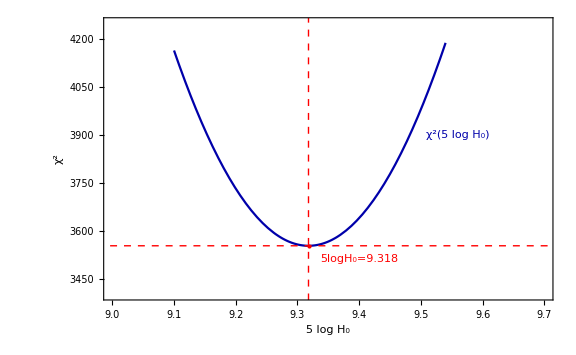

73.0428

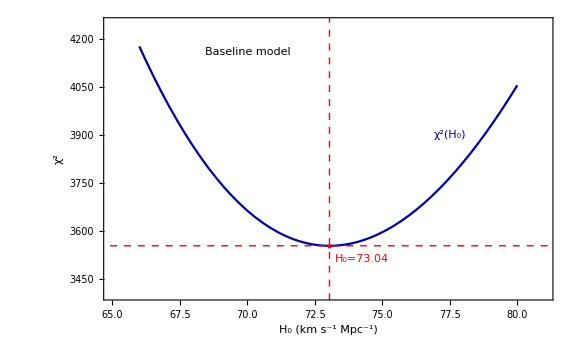

```mathematica
qn[q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_,q9_,q10_,q11_,q12_,q13_,q14_,q15_,q16_,q17_,q18_,q19_,q20_,q21_,q22_,q23_,q24_,q25_,q26_,q27_,q28_,q29_,q30_,q31_,q32_,q33_,q34_,q35_,q36_,q37_,q38_,q39_,q40_,q41_,q42_,q43_,q44_,q45_,q46_,q47_]:={q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14,q15,q16,q17,q18,q19,q20,q21,q22,q23,q24,q25,q26,q27,q28,q29,q30,q31,q32,q33,q34,q35,q36,q37,q38,q39,q40,q41,q42,q43,q44,q45,q46,q47}
vecn[q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_,q9_,q10_,q11_,q12_,q13_,q14_,q15_,q16_,q17_,q18_,q19_,q20_,q21_,q22_,q23_,q24_,q25_,q26_,q27_,q28_,q29_,q30_,q31_,q32_,q33_,q34_,q35_,q36_,q37_,q38_,q39_,q40_,q41_,q42_,q43_,q44_,q45_,q46_,q47_]:=Y-L.qn[q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14,q15,q16,q17,q18,q19,q20,q21,q22,q23,q24,q25,q26,q27,q28,q29,q30,q31,q32,q33,q34,q35,q36,q37,q38,q39,q40,q41,q42,q43,q44,q45,q46,q47]

chi2[q1_,q2_,q3_,q4_,q5_,q6_,q7_,q8_,q9_,q10_,q11_,q12_,q13_,q14_,q15_,q16_,q17_,q18_,q19_,q20_,q21_,q22_,q23_,q24_,q25_,q26_,q27_,q28_,q29_,q30_,q31_,q32_,q33_,q34_,q35_,q36_,q37_,q38_,q39_,q40_,q41_,q42_,q43_,q44_,q45_,q46_,q47_]:=vecn[q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14,q15,q16,q17,q18,q19,q20,q21,q22,q23,q24,q25,q26,q27,q28,q29,q30,q31,q32,q33,q34,q35,q36,q37,q38,q39,q40,q41,q42,q43,q44,q45,q46,q47].InvCall.vecn[q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14,q15,q16,q17,q18,q19,q20,q21,q22,q23,q24,q25,q26,q27,q28,q29,q30,q31,q32,q33,q34,q35,q36,q37,q38,q39,q40,q41,q42,q43,q44,q45,q46,q47 ]
(*The form of χ2(H0) for the SH0ES baseline model has a minimum at the analytically
predicted value of H0 (the rest of the parameters were fixed at their analytically predicted best fit values). *)
chi2h01[x_]:=chi2[qbf[[1]],qbf[[2]],qbf[[3]],qbf[[4]],qbf[[5]],qbf[[6]],qbf[[7]],qbf[[8]],qbf[[9]],qbf[[10]],qbf[[11]],qbf[[12]],qbf[[13]],qbf[[14]],qbf[[15]],qbf[[16]],qbf[[17]],qbf[[18]],qbf[[19]],qbf[[20]],qbf[[21]],qbf[[22]],qbf[[23]],qbf[[24]],qbf[[25]],qbf[[26]],qbf[[27]],qbf[[28]],qbf[[29]],qbf[[30]],qbf[[31]],qbf[[32]],qbf[[33]],qbf[[34]],qbf[[35]],qbf[[36]],qbf[[37]],qbf[[38]],qbf[[39]],qbf[[40]],qbf[[41]],qbf[[42]],qbf[[43]],qbf[[44]],qbf[[45]],qbf[[46]],x]

plchi2h01=Plot[chi2h01[x],{x,9.1,9.54},Frame->True,FrameLabel->{"5 log H_0 ","χ^2"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{9,9.7},{3400,4250}},Axes->False,PlotStyle->{Darker[Blue]},ImageSize->Large, FrameStyle -> Directive[Black, Thick,16],Epilog->{{Inset[Style["Baseline model",Black],{70,4160}]},{Inset[Style["5logH_0=9.318",Red],{9.4,3510}]},{Inset[Style["χ^2(5 log H_0)",Darker[Blue]],{9.56,3900}]},{PointSize[Large],Red,Point[{qbf[[47]],3552.75933}]},{Dashing[{Small,Small}],Thickness[Medium],Red,Line[{{qbf[[47]],3000},{qbf[[47]],5000}}]},{Dashing[{Small,Small}],Thickness[Medium],Red,Line[{{0,3552.75933029552},{100,3552.75933029552}}]}}]
h0=10^(qbf[[47]]/5)
chi2h02[h0_]:=chi2[qbf[[1]],qbf[[2]],qbf[[3]],qbf[[4]],qbf[[5]],qbf[[6]],qbf[[7]],qbf[[8]],qbf[[9]],qbf[[10]],qbf[[11]],qbf[[12]],qbf[[13]],qbf[[14]],qbf[[15]],qbf[[16]],qbf[[17]],qbf[[18]],qbf[[19]],qbf[[20]],qbf[[21]],qbf[[22]],qbf[[23]],qbf[[24]],qbf[[25]],qbf[[26]],qbf[[27]],qbf[[28]],qbf[[29]],qbf[[30]],qbf[[31]],qbf[[32]],qbf[[33]],qbf[[34]],qbf[[35]],qbf[[36]],qbf[[37]],qbf[[38]],qbf[[39]],qbf[[40]],qbf[[41]],qbf[[42]],qbf[[43]],qbf[[44]],qbf[[45]],qbf[[46]],5*Log[10,h0]]
plchi2h02=Plot[chi2h02[h0],{h0,66,80},Frame->True,FrameLabel->{"H_0 (km s^-1 Mpc^-1)","χ^2"},BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{65,81},{3400,4250}},Axes->False,PlotStyle->{Darker[Blue]},ImageSize->Large, FrameStyle -> Directive[Black, Thick,16],Epilog->{{Inset[Style["Baseline model",Black],{70,4160}]},{Inset[Style["H_0=73.04",Red],{74.24,3510}]},{Inset[Style["χ^2(H_0)",Darker[Blue]],{77.5,3900}]},{PointSize[Large],Red,Point[{73.0428,3552.75933}]},{Dashing[{Small,Small}],Thickness[Medium],Red,Line[{{73.0428,3000},{73.0428,5000}}]},{Dashing[{Small,Small}],Thickness[Medium],Red,Line[{{0,3552.75933029552},{100,3552.75933029552}}]}}]
```

```mathematica
Export[NotebookDirectory[]<>"plchi2h02.pdf",plchi2h02,ImageResolution->1000];
```

```mathematica
(* We demonstrate the full consistency of our results with the full numerical minimization of χ^2 *)
```

```mathematica
chi2min=FindMinimum[chi2[q1,q2,q3,q4,q5,q6,q7,q8,q9,q10,q11,q12,q13,q14,q15,q16,q17,q18,q19,q20,q21,q22,q23,q24,q25,q26,q27,q28,q29,q30,q31,q32,q33,q34,q35,q36,q37,q38,q39,q40,q41,q42,q43,q44,q45,q46,q47],{q1,qbf[[1]]},{q2,qbf[[2]]},{q3,qbf[[3]]},{q4,qbf[[4]]},{q5,qbf[[5]]},{q6,qbf[[6]]},{q7,qbf[[7]]},{q8,qbf[[8]]},{q9,qbf[[9]]},{q10,qbf[[10]]},{q11,qbf[[11]]},{q12,qbf[[12]]},{q13,qbf[[13]]},{q14,qbf[[14]]},{q15,qbf[[15]]},{q16,qbf[[16]]},{q17,qbf[[17]]},{q18,qbf[[18]]},{q19,qbf[[19]]},{q20,qbf[[20]]},{q21,qbf[[21]]},{q22,qbf[[22]]},{q23,qbf[[23]]},{q24,qbf[[24]]},{q25,qbf[[25]]},{q26,qbf[[26]]},{q27,qbf[[27]]},{q28,qbf[[28]]},{q29,qbf[[29]]},{q30,qbf[[30]]},{q31,qbf[[31]]},{q32,qbf[[32]]},{q33,qbf[[33]]},{q34,qbf[[34]]},{q35,qbf[[35]]},{q36,qbf[[36]]},{q37,qbf[[37]]},{q38,qbf[[38]]},{q39,qbf[[39]]},{q40,qbf[[40]]},{q41,qbf[[41]]},{q42,qbf[[42]]},{q43,qbf[[43]]},{q44,qbf[[44]]},{q45,qbf[[45]]},{q46,qbf[[46]]},{q47,qbf[[47]]}]
```

{3552.76,{q1→29.1596,q2→32.9156,q3→32.8222,q4→32.6178,q5→34.4934,q6→32.509,q7→31.3254,q8→31.2951,q9→31.4608,q10→31.4652,q11→32.0114,q12→32.6278,q13→32.3916,q14→33.0908,q15→32.4031,q16→32.1425,q17→31.9443,q18→32.7899,q19→31.7072,q20→31.6382,q21→31.6338,q22→30.8239,q23→30.8355,q24→31.7874,q25→32.5468,q26→33.1873,q27→31.8655,q28→30.5084,q29→32.9159,q30→32.2052,q31→32.3369,q32→31.606,q33→33.2692,q34→32.5797,q35→33.2669,q36→33.5439,q37→32.816,q38→-0.0127018,q39→-5.89352,q40→0.0100843,q41→24.3714,q42→-0.0135244,q43→-19.2529,q44→-0.216585,q45→0.,q46→-0.0738103,q47→9.31789}}